```mathematica
Pi/4//N
```

0.785398

```mathematica
Pi/3//N
```

1.0472

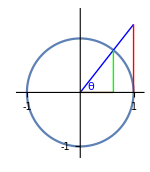

```mathematica
Show[
ParametricPlot[
{Cos[t],Sin[t]},{t,0,2 Pi},ImageSize->100,PlotRange->{{-1.15,1.15},{-1.15,1.5}},Ticks->{{-1,1},{-3,-2,-1,1,2,3}},AspectRatio->2.65/2.3
],
Graphics[
{
Opacity[1],
Blue,Line[{{0,0},{1,Tan[.9]}}],Text[θ,{0.2,0.1}],
Thick, Red,
Line[{{1,0},{1,Tan[.9]}}],Green,
Line[{{Cos[.9],0},{Cos[.9],Sin[.9]}}],Brown,Line[{{0,0},{Cos[.9],0}}]
}
],ImageSize->150
]
```

```mathematica
Manipulate[
Show[
ParametricPlot[
{Cos[t],Sin[t]},{t,0,2 Pi},ImageSize->100,PlotRange->{{-1,1},{-3,3}},Ticks->{{-1,1},{-3,-2,-1,1,2,3}},AspectRatio->3
],
Graphics[
{
Opacity[1],
Blue,
Line[{{0,0},{1,Tan[theta]}}],
Red,
Line[{{1,0},{1,Tan[theta]}}]
}
]
],
{{theta,Pi/6},-Pi/2,Pi/2},SaveDefinitions->True
]
```